```mathematica
2f[x]==g[x]
```

2 f[x]==g[x]

```mathematica
2f[x]
```

2 f[x]

```mathematica
2f[x]==f[x]+f[x]
```

True

```mathematica
f[x]==1/(1+f[x])
```

f[x]==1/(1+f[x])

```mathematica
Reduce[f[x]==1/(1+f[x])]
```

f[x]==1/2 (-1-√5)||f[x]==1/2 (-1+√5)

```mathematica
√5
```

√5

```mathematica
N[√5]
```

2.23607

```mathematica
2f[x]==1/(1+f[x])
```

2 f[x]==1/(1+f[x])

```mathematica
Reduce[2 f[x]==1/(1+f[x])]
```

f[x]==1/2 (-1-√3)||f[x]==1/2 (-1+√3)

```mathematica
ϕ==1/(1+ϕ)
```

ϕ==1/(1+ϕ)

```mathematica
Reduce[ϕ==1/(1+ϕ)]
```

ϕ==1/2 (-1-√5)||ϕ==1/2 (-1+√5)

```mathematica
N[1/2 (-1-√5)]
```

-1.61803

```mathematica
1/(1+1)
```

1/2

```mathematica
NestList[1/(1+#)&,1/2,10]
```

{1/2,2/3,3/5,5/8,8/13,13/21,21/34,34/55,55/89,89/144,144/233}

```mathematica
NestList[N@(1/(1+#))&,1/2,10]
```

{1/2,0.666667,0.6,0.625,0.615385,0.619048,0.617647,0.618182,0.617978,0.618056,0.618026}

```mathematica
NestList[N@(1/(1+#))&,1,10]
```

{1,0.5,0.666667,0.6,0.625,0.615385,0.619048,0.617647,0.618182,0.617978,0.618056}

```mathematica
NestList[N@(1/(1+#))&,1,30]
```

{1,0.5,0.666667,0.6,0.625,0.615385,0.619048,0.617647,0.618182,0.617978,0.618056,0.618026,0.618037,0.618033,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034,0.618034}

```mathematica
NestList[1/(1+#)&,n,10]
```

{n,1/(1+n),1/(1+1/(1+n)),1/(1+1/(1+1/(1+n))),1/(1+1/(1+1/(1+1/(1+n)))),1/(1+1/(1+1/(1+1/(1+1/(1+n))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n)))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n)))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))))))}

```mathematica
NestList[FullSimplify[1/(1+#)&,Element[n,Reals]],n,10]
```

{n,1/(1+n),1/(1+1/(1+n)),1/(1+1/(1+1/(1+n))),1/(1+1/(1+1/(1+1/(1+n)))),1/(1+1/(1+1/(1+1/(1+1/(1+n))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n)))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n)))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))))))}

```mathematica
FullSimplify[
{n,1/(1+n),1/(1+1/(1+n)),1/(1+1/(1+1/(1+n))),1/(1+1/(1+1/(1+1/(1+n)))),1/(1+1/(1+1/(1+1/(1+1/(1+n))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n)))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n)))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))))),1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+1/(1+n))))))))))}
,n∈Reals]
```

{n,1/(1+n),(1+n)/(2+n),(2+n)/(3+2 n),(3+2 n)/(5+3 n),(5+3 n)/(8+5 n),(8+5 n)/(13+8 n),(13+8 n)/(21+13 n),(21+13 n)/(34+21 n),(34+21 n)/(55+34 n),(55+34 n)/(89+55 n)}

```mathematica
FullSimplify[NestList[FullSimplify[1/(1-#)&,Element[n,Reals]],n,10],n∈Reals]
```

{n,1/(1-n),(-1+n)/n,n,1/(1-n),(-1+n)/n,n,1/(1-n),(-1+n)/n,n,1/(1-n)}

```mathematica
Reduce[n==1/(1+n),n,Reals]
```

n==1/2 (-1-√5)||n==1/2 (-1+√5)

```mathematica
Reduce[n==1/(1-n),n,Reals]
```

False

```mathematica
Reduce[1/(1+n)==1/(1+1/(1+n)),n,Reals]
```

n==1/2 (-1-√5)||n==1/2 (-1+√5)

```mathematica
1/(1+x)
```

1/(1+x)

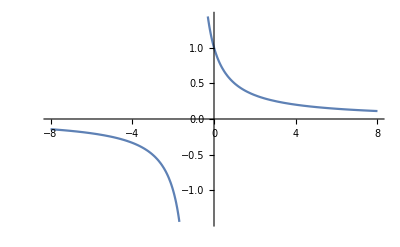

```mathematica
Plot[1/(1+x),{x,-8,8}]
```

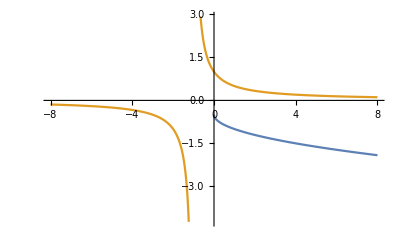

```mathematica
Plot[{1/2(-1-√x),1/(1+x)},{x,-8,8}]
```

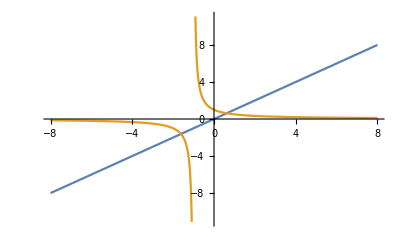

```mathematica
Plot[{x,1/(1+x)},{x,-8,8}]
```

```mathematica
f[x,n]==x^((-1)n)
```

```mathematica
FullSimplify[NestList[FullSimplify[1/#&,Element[n,Reals]],n,10],n∈Reals]
```

{n,1/n,n,1/n,n,1/n,n,1/n,n,1/n,n}

```mathematica
f[x,n]==x^((-1)n)
```

f[x,n]==x^-n

```mathematica
With[{f=Function[{x,n},x^((-1)n)]},
f[x,n]
]
```

x^-n

```mathematica
With[{f=Function[{x,n},x^((-1)n)]},
f[x,0]
]
```

1

```mathematica
With[{f=Function[{x,n},x^((-1)n)]},
f[x,1]
]
```

1/x

```mathematica
With[{f=Function[{x,n},x^((-1)^n)]},
f[x,1]
]
```

1/x

```mathematica
With[{f=Function[{x,n},x^((-1)^n)]},
f[x,0]
]
```

x

```mathematica
With[{f=Function[{x,n},x^((-1)^n)]},
f[x,1]
]
```

1/x

```mathematica
With[{f=Function[{x,n},x^((-1)^(n-1))]},
f[x,1]
]
```

x

```mathematica
With[{f=Function[{x,n},x^((-1)^(n-1))]},
f[x,0]
]
```

1/x

```mathematica
With[{f=Function[{x,n},x^((-1)^(n-1))]},
f[x,2]
]
```

1/x

```mathematica
(-1)^x
```

(-1)^x

```mathematica
Plot[(-1)^x,{x,-1,1}]
```

-Graphics-

```mathematica
With[{f=Function[{x,n},x^((-1)^(n-1))]},
f[x,2]
]
```

```mathematica
With[{f=Function[{x,n},x^((-1)^(n-1))]},
(∂f[x,n])/(∂n)
]
```

Derivative::novar: ∂f[x,n] cannot be interpreted. A partial derivative requires a subscript differentiation variable.

```mathematica
With[{f=Function[{x,n},x^((-1)^(n-1))]},
D[f[x,n], n]
]
```

ⅈ (-1)^(-1+n) π x^((-1)^(-1+n)) Log[x]

```mathematica
Exp[ⅈ]
```

ⅇ^ⅈ

```mathematica
N[ⅇ^ⅈ]
```

0.540302+0.841471 ⅈ

```mathematica
841471/(2π)
```

841471/(2 π)

```mathematica
(.841471)/(2 π)
```

0.133924